```mathematica
(*
Brendan Morgan
905 391 452
Extra Credit, Homework 6 Problem 7
*)

(*This assumes a 2D case, because I believe the inclination of orbits is not very relevant for showing precession.*)
```

```mathematica
Remove["Global`*"]

SetAttributes[{M,G,m1,m2,m3,m4,m5,m6,m7,m8,m9},Constant]; 
$Assumptions = {Element[{G,m1,m2,m3,m4,m5,m6,m7,m8,m9},Reals] && G>0 };

(*Nine Bodies including the Sun*)
NumOfBodies =9;
M ={m1,m2,m3,m4,m5,m6,m7,m8,m9};
X={x1[t],x2[t],x3[t],x4[t],x5[t],x6[t],x7[t],x8[t],x9[t]};
Y={y1[t],y2[t],y3[t],y4[t],y5[t],y6[t],y7[t],y8[t],y9[t]};
dXdt={x1'[t],x2'[t],x3'[t],x4'[t],x5'[t],x6'[t],x7'[t],x8'[t],x9'[t]};
dYdt={y1'[t],y2'[t],y3'[t],y4'[t],y5'[t],y6'[t],y7'[t],y8'[t],y9'[t]};

(*Lagrangian*)
T[i_] := 1/2*M[[i]]*(dXdt[[i]]^2+dYdt[[i]]^2);
TSum :=Sum[T[i],{i,1,NumOfBodies}];

U[i_,j_]:=-G*M[[i]]*M[[j]]/(Sqrt[(X[[i]]-X[[j]])^2+(Y[[i]]-Y[[j]])^2]);
USum := Sum[ Sum[U[i,j],{j,i+1,NumOfBodies}], {i,1,NumOfBodies}];

lag=TSum-USum;

(*Euler-Lagrange to find the Equations of Motion*)l
EL[q_] :=  D[lag,q] - Dt[   D[lag,  D[q,t]], t ] == 0;

ELX[i_]:=EL[X[[i]]];
EqnsOfMotionX=Array[ELX,NumOfBodies];
ELY[i_]:=EL[Y[[i]]];
EqnsOfMotionY=Array[ELY,NumOfBodies];
```

l

```mathematica
(***************************************************************************)

G=6.6743*10^-20;(*km^2 kg^-1 s^-1*)

(*Data from https://nssdc.gsfc.nasa.gov/planetary/factsheet/*)
(*All in kilograms*)
m1=0.330*10^24;(*Mercury*)
m2=4.870*10^24;(*Venus*)
m3=5.970*10^24;(*Earth*)
m4=0.642*10^24;(*Mars*)
m5=1898.*10^24;(*Jupiter*)
m6=568.0*10^24;(*Saturn*)
m7=86.80*10^24;(*Uranus*)
m8=102.0*10^24;(*Neptune*)
m9=1.990*10^30 ;(*Sun*)

(*Planet Orbital Parameters, All in km and km/s*)
X0={x1[0]==46.0*10^6,x2[0]==0,x3[0]==-147.1*10^6,x4[0]==0,x5[0]==740.5*10^6,x6[0]==0,x7[0]==-2741.3*10^6,x8[0]==0,x9[0]==0};
Y0={y1[0]==0,y2[0]==107.5*10^6,y3[0]==0,y4[0]==-206.6*10^6,y5[0]==0,y6[0]==1352.6*10^6,y7[0]==0,y8[0]==-4444.5*10^6,y9[0]==0};
dXdt0={x1'[0]==0,x2'[0]==-35.26,x3'[0]==0,x4'[0]==26.50,x5'[0]==0,x6'[0]==-10.18,x7'[0]==0,x8'[0]==5.50,x9'[0]==0};
dYdt0={y1'[0]==58.98,y2'[0]==0,y3'[0]==-30.29,y4'[0]==0,y5'[0]==13.72,y6'[0]==0,y7'[0]==-7.11,y8'[0]==0,y9'[0]==0};

(*Solving the Equations of Motion*)
EndTime=1000*31557600;(*Years*)
TimeStep=1000;
numeric=NDSolve[{EqnsOfMotionX,EqnsOfMotionY, X0,dXdt0,Y0,dYdt0},{X,Y},{t,0,EndTime,TimeStep}][[1]];
```

```mathematica
SolnX[t_]=X/.numeric;//Simplify 
SolnY[t_]=Y/.numeric;//Simplify 

(*Animating the Solar System*)
Mercury[t_]:=Graphics[{PointSize[0.01],Brown,              Point[{SolnX[t][[1]],SolnY[t][[1]]}]}];
Venus[t_]:=     Graphics[{PointSize[0.01],Orange,           Point[{SolnX[t][[2]],SolnY[t][[2]]}]}];
Earth[t_]:=     Graphics[{PointSize[0.01],Cyan,                Point[{SolnX[t][[3]],SolnY[t][[3]]}]}];
Mars[t_]:=       Graphics[{PointSize[0.01],Red,                   Point[{SolnX[t][[4]],SolnY[t][[4]]}]}];
Jupiter[t_]:=Graphics[{PointSize[0.01],Orange,            Point[{SolnX[t][[5]],SolnY[t][[5]]}]}];
Saturn[t_]:=  Graphics[{PointSize[0.01],Brown,               Point[{SolnX[t][[6]],SolnY[t][[6]]}]}];
Uranus[t_]:=  Graphics[{PointSize[0.01],Cyan,                 Point[{SolnX[t][[7]],SolnY[t][[7]]}]}];
Neptune[t_]:=Graphics[{PointSize[0.01],Blue,                 Point[{SolnX[t][[8]],SolnY[t][[8]]}]}];
Sun[t_]:=         Graphics[{PointSize[0.02],Yellow,             Point[{SolnX[t][[9]],SolnY[t][[9]]}]}];

SolarSystem[t_]={Sun[t],Mercury[t],Venus[t],Earth[t],Mars[t],Jupiter[t],Saturn[t],Uranus[t],Neptune[t]};
WideView[t_]:=Show[SolarSystem[t],Axes->False,PlotRange->{{-5*10^9,5*10^9},{-5*10^9,5*10^9}},Background->Black,ImageSize->Medium,AxesOrigin->{0,0}];
InnerPlanets[t_]:=Show[SolarSystem[t],Axes->False,PlotRange->{{-3*10^8,3*10^8},{-3*10^8,3*10^8}},Background->Black,ImageSize->Medium,AxesOrigin->{0,0}];

Year =31557600;
t1=100*Year;
Animate[WideView[t],{t,0,t1,TimeStep}]
t2=10*Year;
Animate[InnerPlanets[t],{t,0,t2,TimeStep}]
```

The above two animations show the Solar System, the first one with the Sun and all eight planets and the second one with the Sun and just the four inner planets. All planet sizes are clearly not to scale, but distances are indeed to scale.

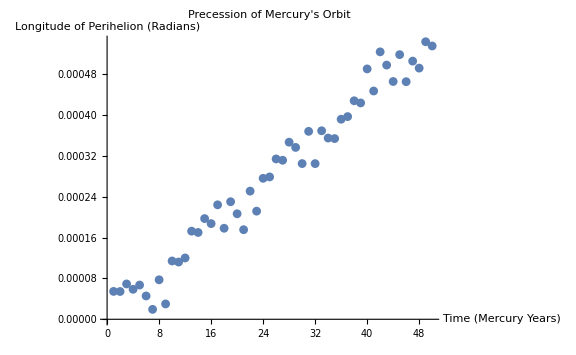

```mathematica
(*This is for Mercury and the Sun, but can easily be modified for other planet by changing the numbers in only the line below*)
RadialDistance[t_]=Sqrt[(SolnX[t][[1]]-SolnX[t][[9]])^2+(SolnY[t][[1]]-SolnY[t][[9]])^2] ;
RadialVelocity[t_] = D[RadialDistance[t],t];

(*Apsides occur when velocity is zero. Every other apside is a perihelion.*)
PeriTimes={};
Period= 87.969*86400; (*Mercury Year*)
For[i=1,i<100,i+=2,
AppendTo[PeriTimes,t/.FindRoot[RadialVelocity[t],{t,Period*(i-0.2),Period*(i+0.2)}]]
]

(*Plotting the longitude of perihelion over time*)
PeriLongitude[t_]=ArcTan[SolnX[t][[1]]-SolnX[t][[9]],SolnY[t][[1]]-SolnY[t][[9]]];
PeriTable = Table[PeriLongitude[t],{t,PeriTimes}];
ListPlot[PeriTable,AxesLabel->{"Time (Mercury Years)","Longitude of Perihelion (Radians)"},PlotLabel->"Precession of Mercury's Orbit",ImageSize->Large]
```

```mathematica
(*Running a Fit to find the rate of Mercury's precession*)

TruePeriod= {};
For[i=1,i<49,i+=1,
AppendTo[TruePeriod,PeriTimes[[i+1]]-PeriTimes[[i]]]
];
MercuryYear=Mean[TruePeriod];

Precession = D[Fit[PeriTable, {t},t],t]; (*Radians/Mercury Year*)
Precession = Precession * (360/(2*Pi)) * (1/MercuryYear)*(100*Year)*(3600); (*Converted to Arcseconds/Century*)

Print["Mercury's Precessional Rate: ", Precession," Arcseconds per Century"]
```

Mercury's Precessional Rate: 471.808 Arcseconds per Century

Final Result of Mercury's precession due to the influence of the other seven planets. The true experimental value is about 532 arcseconds per century. That is an error of about 12.8 percent. I consider this pretty good given I had a multitude of input parameters with only a few significant figures, some as low as three, and a lot of calculations compounding those errors.